## ListPlot Different Labels

#### Callout

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];
ListPlot[(Callout[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in kilometres to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],ImageSize->Full,Frame->True,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

-Graphics-

#### Tooltips

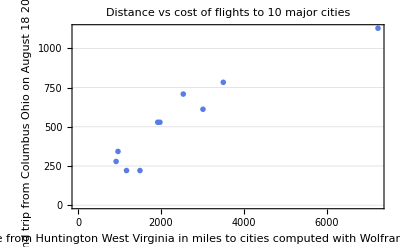

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];
ListPlot[(Tooltip[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],Frame->True,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

#### Legend

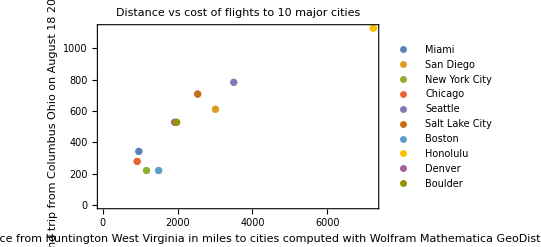

```mathematica
Module[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=List/@AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];
ListPlot[(Legended[travelAssociation[#1],#["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],ImageSize->Scaled[.87],Frame->True,PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

## Final Choice

```mathematica
Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];
ListPlot[(Callout[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],ImageSize->Full,Frame->True,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]]
```

-Graphics-

## Exporting the data to an SVG vector image file

```mathematica
Export["C:\\Users\\peter\\Documents\\Statistics Class Laura Stapleton Summer I\\scatterplot of flight distance in miles and cost on August 18 2022.svg",Rasterize[Block[{cities,travelAssociation},cities={Entity["City",{"Miami","Florida","UnitedStates"}],Entity["City",{"SanDiego","California","UnitedStates"}],Entity["City",{"NewYork","NewYork","UnitedStates"}],Entity["City",{"Chicago","Illinois","UnitedStates"}],Entity["City",{"Seattle","Washington","UnitedStates"}],Entity["City",{"SaltLakeCity","Utah","UnitedStates"}],Entity["City",{"Boston","Massachusetts","UnitedStates"}],Entity["City",{"Honolulu","Hawaii","UnitedStates"}],Entity["City",{"Denver","Colorado","UnitedStates"}],Entity["City",{"Boulder","Colorado","UnitedStates"}]};
travelAssociation=AssociationThread[cities->Transpose[{(GeoDistance[Here,#1,UnitSystem->"Metric"]&)/@cities,{343,612,221,279,784,709,221,1129,529,529}}]];
ListPlot[(Callout[travelAssociation[#1],#1["Name"]]&)/@cities,FrameLabel->{"Geodesic Distance from Huntington West Virginia in miles to cities computed with Wolfram Mathematica GeoDistance","Cost of cheapest round trip from Columbus Ohio on August 18 2022 from Google Flights"},LabelStyle->Directive[FontFamily->"JetBrains Mono"],ImageSize->Full,Frame->True,PlotTheme->"Business",PlotLabel->"Distance vs cost of flights to 10 major cities"]],ImageSize->Full]]
```

C:\Users\peter\Documents\Statistics Class Laura Stapleton Summer I\scatterplot of flight distance in miles and cost on August 18 2022.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\Statistics Class Laura Stapleton Summer I\\scatterplot of flight distance in miles and cost on August 18 2022.svg"]
```